# MinMax Algorithm

Minimax is a kind of backtracking algorithm that is used in decision making and game theory to find the optimal move for a player, assuming that your opponent also plays optimally. It is widely used in two player turn based games such as Tic-Tac-Toe,  Chess, etc.  
In this algorithm, one player is called maximizer and the other is called minimizer. Maximizer tries to get the highest possible score while minimizer  tries to get the lowest. The score is evaluated by the player which is the maximizer and minimizer is usually the opponent. This can be easily expressed as a tree graph where node is a single state of the game and path is action that change the current game state to the next. 
To demonstrate this algorithm, the following graphs will shows how the algorithm works step by step in a 4-ply minmax agent. In this graph, we have a starting state and three possible action that leads to three different states. This is a maximum layer since we as the player should choose action benefits ourself.



```mathematica
TreeGraph[
{1<->2,1<->3,1<->4}]
```

As the game expends,  with each state, the minimizer has two possible action. Each action leads to different states.

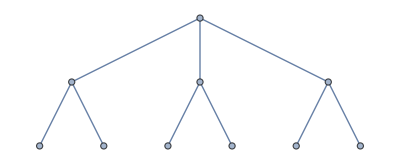

```mathematica
TreeGraph[
{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10}]
```

Then the game is back to the maximizer, with several possible actions.

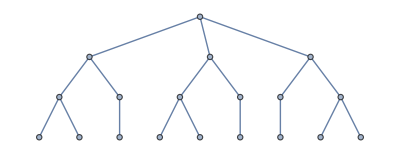

```mathematica
TreeGraph[
{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10,5<->11,5<->12,6<->13,7<->14,7<->15,8<->16,9<->17,10<->18,10<->19}]
```

Then the game goes to minimizer. Since this is a 4-ply agent, it stops expending at step 4 and start evaluating each possible state.

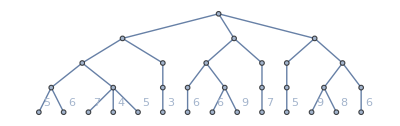

```mathematica
TreeGraph[{
Labeled[20,5],
Labeled[21,6],
Labeled[22,7],
Labeled[23,4],
Labeled[24,5],
Labeled[25,3],
Labeled[26,6],
Labeled[27,6],
Labeled[28,9],
Labeled[29,7],
Labeled[30,5],
Labeled[31,9],
Labeled[32,8],
Labeled[33,6]},
{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10,5<->11,5<->12,6<->13,7<->14,7<->15,8<->16,9<->17,10<->18,10<->19,11<->20,11<->21,12<->22,12<->23,12<->24,13<->25,14<->26,15<->27,15<->28,16<->29,17<->30,18<->31,18<->32,19<->33}]
```

Since the 4th node is a min node which the minimizer decides which action it is going to take, all state with lower score were preferred.

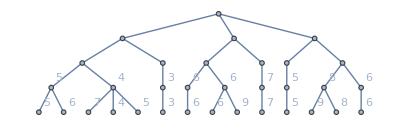

```mathematica
TreeGraph[{
Labeled[11,5],
Labeled[12,4],
Labeled[13,3],
Labeled[14,6],
Labeled[15,6],
Labeled[16,7],
Labeled[17,5],
Labeled[18,8],
Labeled[19,6],
Labeled[20,5],
Labeled[21,6],
Labeled[22,7],
Labeled[23,4],
Labeled[24,5],
Labeled[25,3],
Labeled[26,6],
Labeled[27,6],
Labeled[28,9],
Labeled[29,7],
Labeled[30,5],
Labeled[31,9],
Labeled[32,8],
Labeled[33,6]},
{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10,5<->11,5<->12,6<->13,7<->14,7<->15,8<->16,9<->17,10<->18,10<->19,11<->20,11<->21,12<->22,12<->23,12<->24,13<->25,14<->26,15<->27,15<->28,16<->29,17<->30,18<->31,18<->32,19<->33}]
```

The 3rd node is a max node where the maximizer decides the action. All node with higher score were chosen.

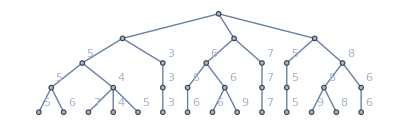

```mathematica
TreeGraph[{
Labeled[5,5],
Labeled[6,3],
Labeled[7,6],
Labeled[8,7],
Labeled[9,5],
Labeled[10,8],
Labeled[11,5],
Labeled[12,4],
Labeled[13,3],
Labeled[14,6],
Labeled[15,6],
Labeled[16,7],
Labeled[17,5],
Labeled[18,8],
Labeled[19,6],
Labeled[20,5],
Labeled[21,6],
Labeled[22,7],
Labeled[23,4],
Labeled[24,5],
Labeled[25,3],
Labeled[26,6],
Labeled[27,6],
Labeled[28,9],
Labeled[29,7],
Labeled[30,5],
Labeled[31,9],
Labeled[32,8],
Labeled[33,6]},
{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10,5<->11,5<->12,6<->13,7<->14,7<->15,8<->16,9<->17,10<->18,10<->19,11<->20,11<->21,12<->22,12<->23,12<->24,13<->25,14<->26,15<->27,15<->28,16<->29,17<->30,18<->31,18<->32,19<->33}]
```

The 2nd node is a min node. Lower scores were selected.

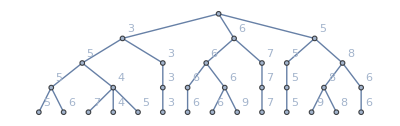

```mathematica
TreeGraph[{
Labeled[2,3],
Labeled[3,6],
Labeled[4,5],
Labeled[5,5],
Labeled[6,3],
Labeled[7,6],
Labeled[8,7],
Labeled[9,5],
Labeled[10,8],
Labeled[11,5],
Labeled[12,4],
Labeled[13,3],
Labeled[14,6],
Labeled[15,6],
Labeled[16,7],
Labeled[17,5],
Labeled[18,8],
Labeled[19,6],
Labeled[20,5],
Labeled[21,6],
Labeled[22,7],
Labeled[23,4],
Labeled[24,5],
Labeled[25,3],
Labeled[26,6],
Labeled[27,6],
Labeled[28,9],
Labeled[29,7],
Labeled[30,5],
Labeled[31,9],
Labeled[32,8],
Labeled[33,6]},
{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10,5<->11,5<->12,6<->13,7<->14,7<->15,8<->16,9<->17,10<->18,10<->19,11<->20,11<->21,12<->22,12<->23,12<->24,13<->25,14<->26,15<->27,15<->28,16<->29,17<->30,18<->31,18<->32,19<->33}]
```

Now we back to the start state and able to know the result of all action when opponent is playing optimal. Since the player is a maximizer, highest result of all three actions will be chosen which is 6.

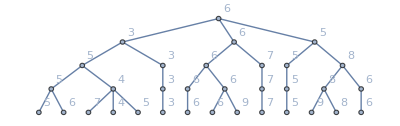

```mathematica
TreeGraph[{Labeled[1,6],
Labeled[2,3],
Labeled[3,6],
Labeled[4,5],
Labeled[5,5],
Labeled[6,3],
Labeled[7,6],
Labeled[8,7],
Labeled[9,5],
Labeled[10,8],
Labeled[11,5],
Labeled[12,4],
Labeled[13,3],
Labeled[14,6],
Labeled[15,6],
Labeled[16,7],
Labeled[17,5],
Labeled[18,8],
Labeled[19,6],
Labeled[20,5],
Labeled[21,6],
Labeled[22,7],
Labeled[23,4],
Labeled[24,5],
Labeled[25,3],
Labeled[26,6],
Labeled[27,6],
Labeled[28,9],
Labeled[29,7],
Labeled[30,5],
Labeled[31,9],
Labeled[32,8],
Labeled[33,6]},
{1<->2,1<->3,1<->4,2<->5,2<->6,3<->7,3<->8,4<->9,4<->10,5<->11,5<->12,6<->13,7<->14,7<->15,8<->16,9<->17,10<->18,10<->19,11<->20,11<->21,12<->22,12<->23,12<->24,13<->25,14<->26,15<->27,15<->28,16<->29,17<->30,18<->31,18<->32,19<->33}]
```

The naive minmax algorithm is able to grantee a best choice if the opponent plays rationally.  The down side of this algorithm is that the search space grows exponentially when the algorithm goes deeper. Different pruning techniques such as AlphaBeta Pruning were used to reduce the search space therefore increase the depth.